## Legendre Polynomials

```mathematica
Subscript[ϕ, 1][x_]=1;
Subscript[ϕ, 2][x_]=√3 x;
Subscript[ϕ, j_][x_]:=Subscript[ϕ, j][x]=(√((2j-3)*(2j-1)))/(j-1)x Subscript[ϕ, j-1][x] - √((2j-1)/(2j-5))(j-2)/(j-1)Subscript[ϕ, j-2][x];
```

```mathematica
M = 12;
Table[1/2∫_-1^1 Subscript[ϕ, i][x]Subscript[ϕ, j][x]ⅆx,{i,1,M},{j,1,M}]==IdentityMatrix[M]
```

True

## Restriction

```mathematica
Subscript[ϕ, 1][x_]=1;
Subscript[ϕ, 2][x_]=√3 x;
Subscript[ϕ, j_][x_]:=Subscript[ϕ, j][x]=(√((2j-3)*(2j-1)))/(j-1)x Subscript[ϕ, j-1][x] - √((2j-1)/(2j-5))(j-2)/(j-1)Subscript[ϕ, j-2][x];
```

```mathematica
M= 5;
Subscript[Q, n_][x_]:=Sum[Subscript[Q, i,n]*Subscript[ϕ, i][x],{i,1,M}];
f[x_] := Piecewise[{{Subscript[Q, 1][2x + 1], x<0}, {Subscript[Q, 2][2x - 1], x>0}}];
rest[j_]:=1/2∫_-1^1 Subscript[ϕ, j][x]f[x]ⅆx
left[j_,i_]:=1/2∫_-1^0 Subscript[ϕ, j][x]Subscript[ϕ, i][2x+1]ⅆx
right[j_,i_]:=1/2∫_0^1 Subscript[ϕ, j][x]Subscript[ϕ, i][2x-1]ⅆx
(*Table[R[i],{i,1,M}]//TableForm*)
L  = Table[left[j,i],{j,1,M},{i,1,M}];
R = Table[right[j,i],{j,1,M},{i,1,M}];
```

```mathematica
L//TableForm
R //TableForm
```

1/2 | 0 | 0 | 0 | 0
-(√3)/4 | 1/4 | 0 | 0 | 0
0 | -(√15)/8 | 1/8 | 0 | 0
(√7)/16 | (√21)/16 | -(√35)/16 | 1/16 | 0
0 | (√3)/16 | (3 √5)/16 | -(3 √7)/32 | 1/32

1/2 | 0 | 0 | 0 | 0
(√3)/4 | 1/4 | 0 | 0 | 0
0 | (√15)/8 | 1/8 | 0 | 0
-(√7)/16 | (√21)/16 | (√35)/16 | 1/16 | 0
0 | -(√3)/16 | (3 √5)/16 | (3 √7)/32 | 1/32

```mathematica
M = 10;
result = "";
For[k =1, k <= M,k++,
result = result <> "case " <> ToString[k] <> ":\n";
For[i = 1, i ≤k,i++,
For[j = 1,j≤k,j++,
If[L[[i,j]]≠0,
result = result <>"    L->set("<>ToString[i]<>","<>ToString[j]<>","<>ToString[N[L[[i,j]],16]]<>");\n"];
];
];
For[i = 1, i ≤k,i++,
For[j = 1,j≤k,j++,
If[R[[i,j]]≠0,result = result <>"    R->set("<>ToString[i]<>","<>ToString[j]<>","<>ToString[N[R[[i,j]],16]]<>");\n"];
];
];
result = result <>"    break;\n";
]
```

```mathematica
Export["~/Desktop/restrict.txt",result]
```

~/Desktop/restrict.txt

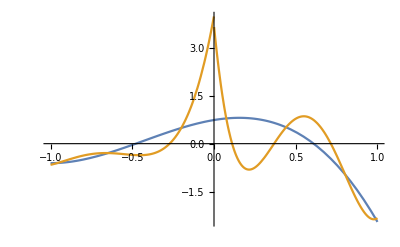

```mathematica
M = 5;
Subscript[ϕ, 1][x_]:=1;
Subscript[ϕ, 2][x_]:=√3 x;
Subscript[ϕ, 3][x_]:=(√5)/2(3 x^2-1)
Subscript[ϕ, 4][x_]:=(√7)/2( 5 x^3-3  x)
Subscript[ϕ, 5][x_]:=105/8 x^4-45/4 x^2+9/8
Q1 = RandomReal[{-1,1},M];
Q2 = RandomReal[{-1,1},M];
Q[x_,QI_]:=Sum[QI[[i]]*Subscript[ϕ, i][x],{i,1,M}];
f[x_] := Piecewise[{{Q[2x + 1,Q1], x<0}, {Q[2x - 1,Q2], x>0}}];
R[j_]:=1/2∫_-1^1 Subscript[ϕ, j][x]f[x]ⅆx
Q3 = Table[R[i],{i,1,M}];
Plot[{Q[x,Q3],f[x]},{x,-1,1}]
```

## Interpolation

```mathematica
Subscript[ϕ, 1][x_]=1;
Subscript[ϕ, 2][x_]=√3 x;
Subscript[ϕ, j_][x_]:=Subscript[ϕ, j][x]=(√((2j-3)*(2j-1)))/(j-1)x Subscript[ϕ, j-1][x] - √((2j-1)/(2j-5))(j-2)/(j-1)Subscript[ϕ, j-2][x];
```

```mathematica
M = 5;
Q[x_]:=Sum[Subscript[Q, i]*Subscript[ϕ, i][x],{i,1,M}];
left[j_,i_]:=1/2∫_-1^1 Subscript[ϕ, j][x]*Subscript[ϕ, i][1/2(x-1)]ⅆx
right[j_,i_]:=1/2∫_-1^1 Subscript[ϕ, j][x]*Subscript[ϕ, i][1/2(x+1)]ⅆx
L = Table[left[j,i],{j,1,M},{i,1,M}]
R = Table[right[j,i],{j,1,M},{i,1,M}]
(*IntM[j_]:=1/2∫_-1^1 Subscript[ϕ, j][x]*Q[1/2(x-1)]ⅆx;
IntP[j_]:=1/2∫_-1^1 Subscript[ϕ, j][x]*Q[1/2(x+1)]ⅆx;
Table[IntM[i],{i,1,M}]//TableForm//Expand;
Table[IntP[i],{i,1,M}]//TableForm//Expand;*)
```

{{1,-(√3)/2,0,(√7)/8,0},{0,1/2,-(√15)/4,(√21)/8,(√3)/8},{0,0,1/4,-(√35)/8,(3 √5)/8},{0,0,0,1/8,-(3 √7)/16},{0,0,0,0,1/16}}

{{1,(√3)/2,0,-(√7)/8,0},{0,1/2,(√15)/4,(√21)/8,-(√3)/8},{0,0,1/4,(√35)/8,(3 √5)/8},{0,0,0,1/8,(3 √7)/16},{0,0,0,0,1/16}}

Interpolation

```mathematica
L//TableForm
R //TableForm
```

1 | -(√3)/2 | 0 | (√7)/8 | 0
0 | 1/2 | -(√15)/4 | (√21)/8 | (√3)/8
0 | 0 | 1/4 | -(√35)/8 | (3 √5)/8
0 | 0 | 0 | 1/8 | -(3 √7)/16
0 | 0 | 0 | 0 | 1/16

1 | (√3)/2 | 0 | -(√7)/8 | 0
0 | 1/2 | (√15)/4 | (√21)/8 | -(√3)/8
0 | 0 | 1/4 | (√35)/8 | (3 √5)/8
0 | 0 | 0 | 1/8 | (3 √7)/16
0 | 0 | 0 | 0 | 1/16

Restriction

```mathematica
L//TableForm
R //TableForm
```

1/2 | 0 | 0 | 0 | 0
-(√3)/4 | 1/4 | 0 | 0 | 0
0 | -(√15)/8 | 1/8 | 0 | 0
(√7)/16 | (√21)/16 | -(√35)/16 | 1/16 | 0
0 | (√3)/16 | (3 √5)/16 | -(3 √7)/32 | 1/32

1/2 | 0 | 0 | 0 | 0
(√3)/4 | 1/4 | 0 | 0 | 0
0 | (√15)/8 | 1/8 | 0 | 0
-(√7)/16 | (√21)/16 | (√35)/16 | 1/16 | 0
0 | -(√3)/16 | (3 √5)/16 | (3 √7)/32 | 1/32

```mathematica
M = 10;
result = "    switch(space_order){\n";
For[k =1, k <= M,k++,
result = result <> "        case " <> ToString[k] <> ":\n";
For[i = 1, i ≤k,i++,
For[j = 1,j≤k,j++,
If[L[[i,j]]≠0,
result = result <>"            L->set("<>ToString[i]<>","<>ToString[j]<>","<>ToString[N[L[[i,j]],16]]<>");\n"];
];
];
For[i = 1, i ≤k,i++,
For[j = 1,j≤k,j++,
If[R[[i,j]]≠0,result = result <>"            R->set("<>ToString[i]<>","<>ToString[j]<>","<>ToString[N[R[[i,j]],16]]<>");\n"];
];
];
result = result <>"            break;\n";
];
result  = result <> "    }\n";
Export["~/Desktop/interpolate.txt",result]
```

~/Desktop/interpolate.txt

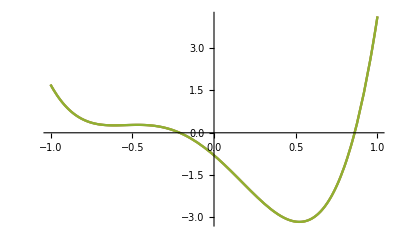

```mathematica
M = 5;
Subscript[ϕ, 1][x_]:=1;
Subscript[ϕ, 2][x_]:=√3 x;
Subscript[ϕ, 3][x_]:=(√5)/2(3 x^2-1)
Subscript[ϕ, 4][x_]:=(√7)/2( 5 x^3-3  x)
Subscript[ϕ, 5][x_]:=105/8 x^4-45/4 x^2+9/8
QT = RandomReal[{-1,1},M];
Q[x_,QI_]:=Sum[QI[[i]]*Subscript[ϕ, i][x],{i,1,M}];
IntM[j_]:=1/2∫_-1^1 Subscript[ϕ, j][x]*Q[1/2(x-1),QT]ⅆx
IntP[j_]:=1/2∫_-1^1 Subscript[ϕ, j][x]*Q[1/2(x+1),QT]ⅆx
QM = Table[IntM[i],{i,1,M}];
QP = Table[IntP[i],{i,1,M}];
Plot[{Q[x,QT],Q[2x+1,QM],Q[2x-1,QP]},{x,-1,1}]
```